```mathematica
Pi/4.
```

0.785398

```mathematica
Pi/3.`20
```

1.0471975511965977462

```mathematica
Pi/2.
```

1.5708

```mathematica
f[x_]:=Cos[x]
```

```mathematica
f[0.7854]
```

0.707105

```mathematica
f[1.047]
```

0.500171

```mathematica
f[1.571]
```

-0.000203673

```mathematica
d1=f'[0.7854]
```

-0.707108

```mathematica
d2=(f[1.047]-f[0.7854])/(1.047-0.7854)
```

-0.791034

```mathematica
d3=f'[1.047]
```

-0.865927

```mathematica
d4=(f[1.571]-f[1.047])/(1.571-1.047)
```

-0.954914

```mathematica
d5=f'[1.571]
```

-1.

```mathematica
d12=(d2-d1)/(1.047-0.7854)
```

-0.320816

```mathematica
d23=(d3-d2)/(1.047-0.7854)
```

-0.286288

```mathematica
d34=(d4-d3)/(1.571-1.047)
```

-0.169823

```mathematica
d45=(d5-d4)/(1.571-1.047)
```

-0.0860426

```mathematica
d1223=(d23-d12)/(1.047-0.7854)
```

0.13199

```mathematica
d2334=(d34-d23)/(1.571-0.7854)
```

0.14825

```mathematica
d3445=(d45-d34)/(1.571-1.047)
```

0.159885

```mathematica
d122334=(d2334-d1223)/(1.571-0.7854)
```

0.0206985

```mathematica
d233445=(d3445-d2334)/(1.571-0.7854)
```

0.0148105

```mathematica
(d233445-d122334)/(1.571-0.7854)
```

-0.00749493

```mathematica
0.707105-0.707108 (x-0.7854)-0.320816(x-0.7854)^2 + 0.13199 (x-0.7854)^2 (x-1.047)+0.0206985 (x-0.7854)^2 (x-1.047)^2-0.00749493(x-0.7854)^2 (x-1.047)^2 (x-1.571)
```

0.707105-0.707108 (-0.7854+x)-0.320816 (-0.7854+x)^2+0.13199 (-1.047+x) (-0.7854+x)^2+0.0206985 (-1.047+x)^2 (-0.7854+x)^2-0.00749493 (-1.571+x) (-1.047+x)^2 (-0.7854+x)^2

```mathematica
Expand[%]
```

1.00128-0.0076067 x-0.481312 x^2-0.0245092 x^3+0.0599405 x^4-0.00749493 x^5

```mathematica
H5[x_]:=1.001284409971347-0.007606698654371469 x-0.48131215706190705 x^2-0.024509197228928803 x^3+0.059940454494 x^4-0.00749493 x^5
```

```mathematica
H5[x]
```

1.00128-0.0076067 x-0.481312 x^2-0.0245092 x^3+0.0599405 x^4-0.00749493 x^5

```mathematica
f''''''[x]
```

-Cos[x]

```mathematica
6!
```

720

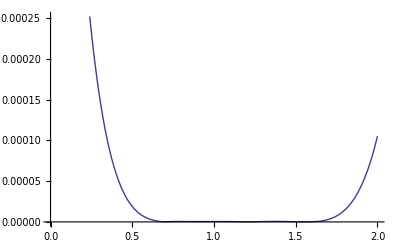

```mathematica
Plot[Abs[f[x]-H5[x]],{x,0,2}]
```

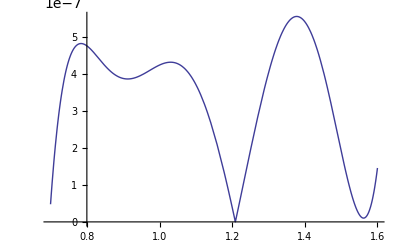

```mathematica
Plot[Abs[f[x]-H5[x]],{x,0.7,1.6}]
```

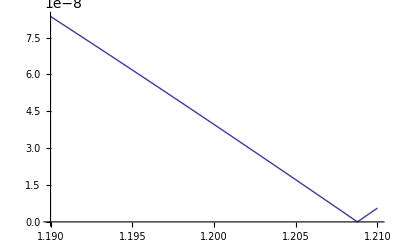

```mathematica
Plot[Abs[f[x]-H5[x]],{x,1.19,1.21}]
```

```mathematica
H5[1.2]
```

0.362358

```mathematica
1/720(1.2-0.7854)^2(1.2-1.047)^2(1.2-1.571)^2
```

7.69231×10^-7